```mathematica
t11 = ({{28, 0, 11}, {30, 0, 2}, {31, 2, 7}, {32, 0, 4}, {34, 0, 2}, {35, 0, 3}, {36, 2, 2}, {39, 4, 0}, {39, 2, 0}, {42, 4, 0}, {43, 5, 0}, {44, 2, 0}, {45, 6, 1}, {47, 5, 2}, {48, 1, 1}, {49, 6, 2}, {51, 5, 2}, {54, 1, 5}, {55, 0, 2}, {56, 0, 5}, {58, 0, 2}, {60, 0, 4}, {60, 0, 5}, {61, 0, 3}, {63, 0, 4}, {63, 6, 0}, {76, 9, 0}, {79, 5, 0}, {81, 10, 3}, {83, 22, 3}, {86, 1, 1}, {87, 6, 4}, {88, 4, 6}, {91, 7, 12}, {93, 2, 10}, {96, 0, 8}, {97, 1, 15}, {98, 0, 4}, {99, 2, 3}, {101, 0, 3}, {103, 4, 0}, {106, 2, 0}, {107, 1, 0}, {109, 1, 0}, {110, 2, 4}, {111, 0, 0}, {112, 1, 0}, {115, 0, 2}, {117, 0, 0}, {118, 1, 1}, {119, 0, 0}, {120, 0, 0}, {121, 0, 0}, {121, 0, 1}, {123, 0, 1}, {125, 0, 1}, {141, 7, 0}, {143, 7, 0}, {145, 20, 0}, {147, 8, 0}, {149, 5, 0}, {150, 2, 0}, {151, 3, 1}, {152, 1, 2}, {156, 0, 10}, {158, 4, 13}, {160, 0, 0}, {161, 2, 4}, {162, 4, 10}, {164, 0, 2}, {165, 1, 8}, {166, 0, 4}, {167, 0, 2}, {168, 1, 3}, {169, 2, 0}, {170, 0, 0}, {171, 0, 0}, {172, 2, 0}, {173, 1, 0}, {174, 10, 0}, {176, 3, 2}, {178, 1, 0}, {179, 6, 0}, {181, 4, 5}})
```

(28 | 0 | 11
30 | 0 | 2
31 | 2 | 7
32 | 0 | 4
34 | 0 | 2
35 | 0 | 3
36 | 2 | 2
39 | 4 | 0
39 | 2 | 0
42 | 4 | 0
43 | 5 | 0
44 | 2 | 0
45 | 6 | 1
47 | 5 | 2
48 | 1 | 1
49 | 6 | 2
51 | 5 | 2
54 | 1 | 5
55 | 0 | 2
56 | 0 | 5
58 | 0 | 2
60 | 0 | 4
60 | 0 | 5
61 | 0 | 3
63 | 0 | 4
63 | 6 | 0
76 | 9 | 0
79 | 5 | 0
81 | 10 | 3
83 | 22 | 3
86 | 1 | 1
87 | 6 | 4
88 | 4 | 6
91 | 7 | 12
93 | 2 | 10
96 | 0 | 8
97 | 1 | 15
98 | 0 | 4
99 | 2 | 3
101 | 0 | 3
103 | 4 | 0
106 | 2 | 0
107 | 1 | 0
109 | 1 | 0
110 | 2 | 4
111 | 0 | 0
112 | 1 | 0
115 | 0 | 2
117 | 0 | 0
118 | 1 | 1
119 | 0 | 0
120 | 0 | 0
121 | 0 | 0
121 | 0 | 1
123 | 0 | 1
125 | 0 | 1
141 | 7 | 0
143 | 7 | 0
145 | 20 | 0
147 | 8 | 0
149 | 5 | 0
150 | 2 | 0
151 | 3 | 1
152 | 1 | 2
156 | 0 | 10
158 | 4 | 13
160 | 0 | 0
161 | 2 | 4
162 | 4 | 10
164 | 0 | 2
165 | 1 | 8
166 | 0 | 4
167 | 0 | 2
168 | 1 | 3
169 | 2 | 0
170 | 0 | 0
171 | 0 | 0
172 | 2 | 0
173 | 1 | 0
174 | 10 | 0
176 | 3 | 2
178 | 1 | 0
179 | 6 | 0
181 | 4 | 5)

```mathematica
Dimensions[t11]
```

{84,3}

```mathematica
MatrixForm[s11=Table[If[j==1,t11[[i,1]],30+Sum[t11[[n,2]]-t11[[n,3]],{n,1,i}]],{i,84},{j,2}]]
```

(28 | 19
30 | 17
31 | 12
32 | 8
34 | 6
35 | 3
36 | 3
39 | 7
39 | 9
42 | 13
43 | 18
44 | 20
45 | 25
47 | 28
48 | 28
49 | 32
51 | 35
54 | 31
55 | 29
56 | 24
58 | 22
60 | 18
60 | 13
61 | 10
63 | 6
63 | 12
76 | 21
79 | 26
81 | 33
83 | 52
86 | 52
87 | 54
88 | 52
91 | 47
93 | 39
96 | 31
97 | 17
98 | 13
99 | 12
101 | 9
103 | 13
106 | 15
107 | 16
109 | 17
110 | 15
111 | 15
112 | 16
115 | 14
117 | 14
118 | 14
119 | 14
120 | 14
121 | 14
121 | 13
123 | 12
125 | 11
141 | 18
143 | 25
145 | 45
147 | 53
149 | 58
150 | 60
151 | 62
152 | 61
156 | 51
158 | 42
160 | 42
161 | 40
162 | 34
164 | 32
165 | 25
166 | 21
167 | 19
168 | 17
169 | 19
170 | 19
171 | 19
172 | 21
173 | 22
174 | 32
176 | 33
178 | 34
179 | 40
181 | 39)

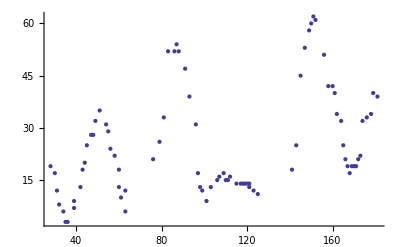

```mathematica
ListPlot[s11]
```

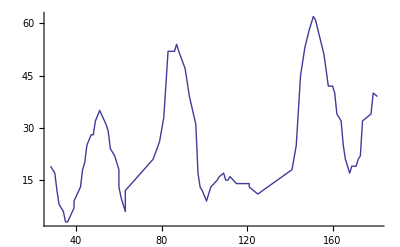

```mathematica
ListPlot[s11,Joined->True]
```

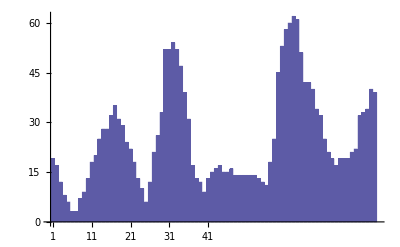

```mathematica
BarChart[s11 [[All, 2 ]]]
```

```mathematica
NotebookDirectory[]
```

W:\SVN\AleviaSpace\projects\nano-misc-todo\my_nb_files\nbfiles\

```mathematica
MatrixForm[t111=Import["data/1term11.txt","Table", Path -> NotebookDirectory[]]]
```

(28 | 0 | 11
30 | 0 | 2
31 | 2 | 7
32 | 0 | 4
34 | 0 | 2
35 | 0 | 3
36 | 2 | 2
39 | 4 | 0
39 | 2 | 0
42 | 4 | 0
43 | 5 | 0
44 | 2 | 0
45 | 6 | 1
47 | 5 | 2
48 | 1 | 1
49 | 6 | 2
51 | 5 | 2
54 | 1 | 5
55 | 0 | 2
56 | 0 | 5
58 | 0 | 2
60 | 0 | 4
60 | 0 | 5
61 | 0 | 3
63 | 0 | 4
63 | 6 | 0
76 | 9 | 0
79 | 5 | 0
81 | 10 | 3
83 | 22 | 3
86 | 1 | 1
87 | 6 | 4
88 | 4 | 6)

```mathematica
Dimensions[t111]
```

{33,3}

```mathematica
MatrixForm[t112=Import["data/1term12.txt","Table", Path -> NotebookDirectory[]]]
```

(91 | 7 | 12
93 | 2 | 10
96 | 0 | 8
97 | 1 | 15
98 | 0 | 4
99 | 2 | 3
101 | 0 | 3
103 | 4 | 0
106 | 2 | 0
107 | 1 | 0
109 | 1 | 0
110 | 2 | 4
111 | 0 | 0
112 | 1 | 0
115 | 0 | 2
117 | 0 | 0
118 | 1 | 1
119 | 0 | 0
120 | 0 | 0
121 | 0 | 0
121 | 0 | 1
123 | 0 | 1
125 | 0 | 1
141 | 7 | 0
143 | 7 | 0
145 | 20 | 0
147 | 8 | 0
149 | 5 | 0
150 | 2 | 0
151 | 3 | 1
152 | 1 | 2)

```mathematica
Dimensions[t112]
```

{31,3}

```mathematica
MatrixForm[t113=Import["data/1term13.txt","Table", Path -> NotebookDirectory[]]]
```

(156 | 0 | 10
158 | 4 | 13
160 | 0 | 0
161 | 2 | 4
162 | 4 | 10
164 | 0 | 2
165 | 1 | 8
166 | 0 | 4
167 | 0 | 2
168 | 1 | 3
169 | 2 | 0
170 | 0 | 0
171 | 0 | 0
172 | 2 | 0
173 | 1 | 0
174 | 10 | 0
176 | 3 | 2
178 | 1 | 0
179 | 6 | 0
181 | 4 | 5)

```mathematica
Dimensions[t113]
```

{20,3}

```mathematica
MatrixForm[s111=Table[If[j==1,t111[[i,1]],30+Sum[t111[[n,2]]-t111[[n,3]],{n,1,i}]],{i,33},{j,2}]];
MatrixForm[s112=Table[If[j==1,t112[[i,1]]-63,52+Sum[t112[[n,2]]-t112[[n,3]],{n,1,i}]],{i,31},{j,2}]];
MatrixForm[s113=Table[If[j==1,t113[[i,1]]-128,61+Sum[t113[[n,2]]-t113[[n,3]],{n,1,i}]],{i,20},{j,2}]];
```

```mathematica
<<"ErrorBarPlots`";<<"PlotLegends`"
```

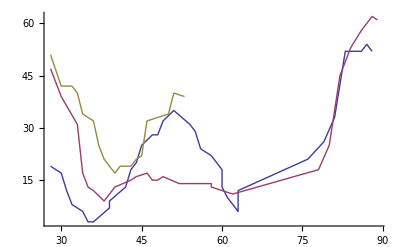

```mathematica
ListPlot[{s111,s112,s113},PlotLegend->{"First","Second","Third"},LegendPosition-> {1, -0.1}, Joined->True]
```

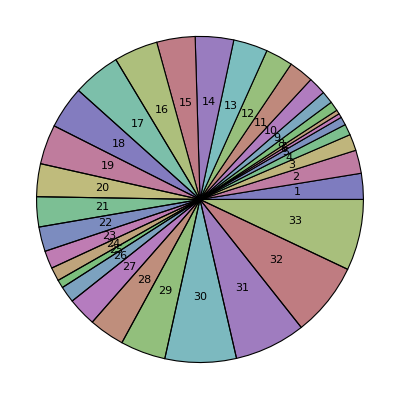

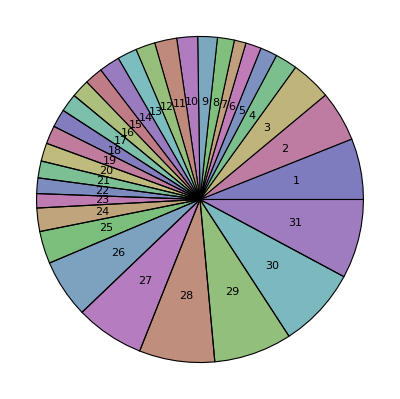

```mathematica
PieChart[Table[s111[[All,2]]]]
PieChart[Table[s112[[All,2]]]]
```